```mathematica
Solve[{0==r*z*Exp[-b*z],0==p*y+(1-m)*z},{y,z}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→0,z→0}}

```mathematica
FullSimplify[r*z*Exp[-b*z]/.{z->(1/b)*Log[p*r/m]}]
```

(m Log[(p r)/m])/(b p)

```mathematica
FullSimplify[(p*y+(1-m)*z)/.{z->(1/b)*Log[p*r/m],y->m*Log[p*r/m]/(b*p)}]
```

Log[(p r)/m]/b

```mathematica
J=({{D[r*z*Exp[-b*z],y], D[r*z*Exp[-b*z],z]}, {D[p*y+(1-m)*z,y], D[p*y+(1-m)*z,z]}})
```

{{0,ⅇ^(-b z) r-b ⅇ^(-b z) r z},{p,1-m}}

```mathematica
MatrixForm[J]
```

(0 | ⅇ^(-b z) r-b ⅇ^(-b z) r z
p | 1-m)

```mathematica
J/.{y->0,z->0}
```

{{0,r},{p,1-m}}

```mathematica
Eigenvalues[{{0,r},{p,1-m}}]
```

{1/2 (1-m-√(1-2 m+m^2+4 p r)),1/2 (1-m+√(1-2 m+m^2+4 p r))}

```mathematica
Det[J/.{y->0,z->0}]
```

-p r

```mathematica
Tr[J/.{y->0,z->0}]
```

1-m

```mathematica
J/.{z->Log[(p r)/m]/b}
```

{{0,m/p-(m Log[(p r)/m])/p},{p,1-m}}

```mathematica
MatrixForm[{{0,m/p-(m Log[(p r)/m])/p},{p,1-m}}]
```

(0 | m/p-(m Log[(p r)/m])/p
p | 1-m)

```mathematica
Det[{{0,m/p-(m Log[(p r)/m])/p},{p,1-m}}]
```

-m+m Log[(p r)/m]

```mathematica
Tr[{{0,m/p-(m Log[(p r)/m])/p},{p,1-m}}]
```

1-m

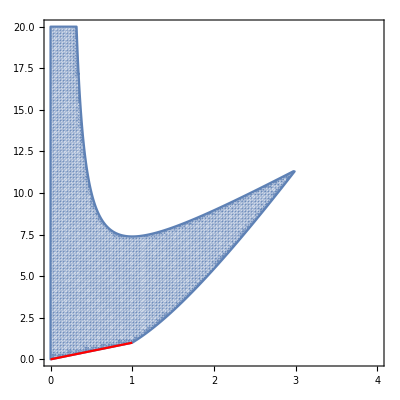

```mathematica
Show[{RegionPlot[Abs[1-m]<1-m+m*Log[s/m]<2,{m,0,4},{s,0,20},PlotPoints->100],Plot[x,{x,0,1},PlotStyle->Red]}]
```

```mathematica
Solve[2*mu-2==mu*Log[s]-mu*Log[mu],s]
```

{{s→ConditionalExpression[ⅇ^((-2+2 mu+mu Log[mu])/mu), -π<Im[(-2+2 mu+mu Log[mu])/mu]≤π]}}

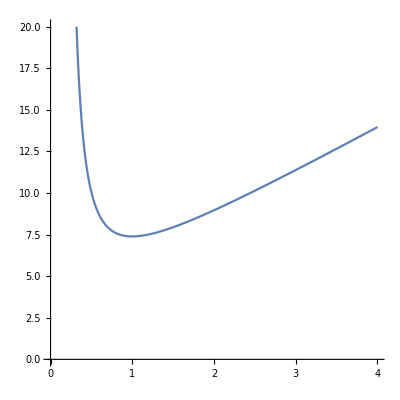

```mathematica
Plot[x*Exp[(1+x)/x],{x,0,4},PlotRange->{{0,4},{0,20}},AspectRatio->1]
```